## DIG 120: Programming in the Humanities Davidson College Dr. Jakub Kabala

Excellent work. In problem #4, notice that ChartStyle→{Red,Blue} is sufficient. Remember also about the ImageSize-> option.
A

## Quiz 2

### Guidelines:

You must work alone.

You have 120 min to complete the quiz. Time begins once you open the Quiz notebook.

This is an open-book quiz: you may consult the Help files in Mathematica, course notes, etc.

Due by Friday, Feb 5th, 5 PM in the Moodle Assignment drop.

Fill out the Honor Pledge below

### Honor Pledge (must be signed before you submit):

“I pledge that in completing the problems below I have followed the instructions above and adhered to the standards of the Davidson Honor Code.”

Time & date begun: 2:15
Time & date ended: 3:20
Total time spent: 1:05
Your name: Kate Gilman

### Problems

The function Row[...] is very similar to Column[...]. Look it up in the Helpfiles. Then make a Row of pie charts with 1, 2 and 3 identical segments:

-Graphics--Graphics--Graphics-

```mathematica
Row[{PieChart[{1,1,1}],PieChart[{1,1}],PieChart[{1}]}]
```

-Graphics--Graphics--Graphics-

You can use the Graphics[...] function to create and style shapes. Here, for example, is a red disk:



```mathematica
Graphics[{Red,Disk[]}]
```

and here is a blue triangle:

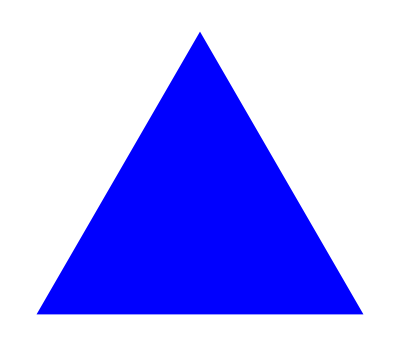

```mathematica
Graphics[{Blue,RegularPolygon[3]}]
```

The function Framed[...], meanwhile, will... put a frame around anything. For example:

```mathematica
Framed["hello"]
```

hello

Study all the code above. Then, using a combination of Row[...], Column[...], Graphics[...], and Framed[...], create the following output (NB: the polygons are pentagons...):

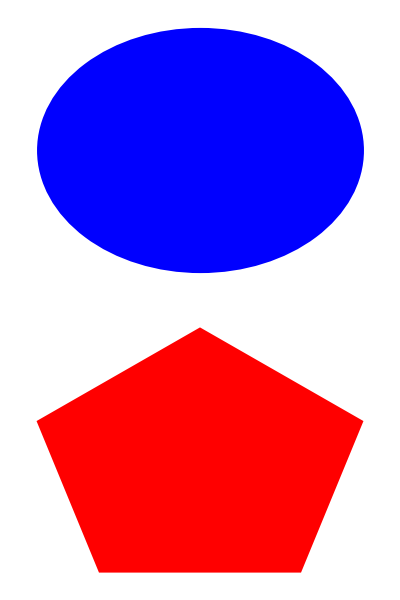
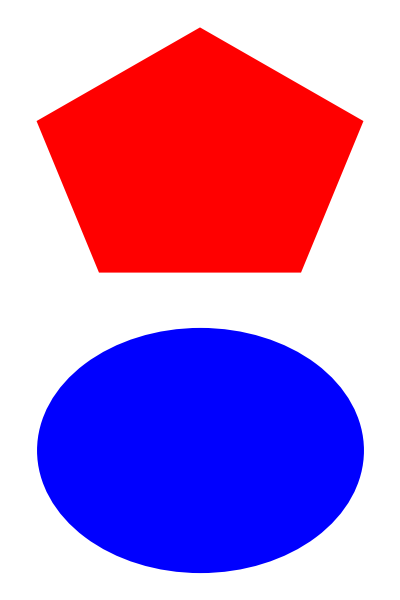

```mathematica
Row[{Graphics[{Blue,Disk}],Graphics[{Red,Polygon[5]}]}]
```

```mathematica
Graphics[{Red,Polygon}]
```

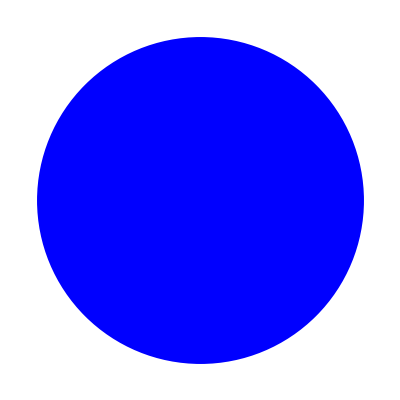
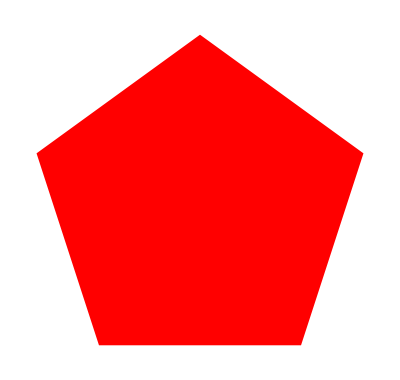

```mathematica
Column[{Row[{Graphics[{Blue,Disk[]}],Graphics[{Red,RegularPolygon[5]}]}]},Row[Graphics[{Red,RegularPolygon[5]}],{Graphics[{Blue,Disk[]}]}]]
```

```mathematica
Framed[Column[{Row[{Graphics[{Blue,Disk[]}],Graphics[{Red,RegularPolygon[5]}]}],Row[{Graphics[{Red,RegularPolygon[5]}],Graphics[{Blue,Disk[]}]}]}]]
```

-Graphics--Graphics-
-Graphics--Graphics-

Here is a list representing the numbers gold medals won by the United States at each Summer Olympics going back to 1984:

```mathematica
medals={83,36,37,44,37,36,36,46,46}
```

```mathematica
{83,36,37,44,37,36,36,46,46}
```

```mathematica
medals
```

{83,36,37,44,37,36,36,46,46}

Using Range[ ...], generate the following list, which contains the actual years in which Summer Olympics have been held going back to 1984. Save that list  it into a symbol called ' years' .

	{1984, 1988, 1992, 1996, 2000, 2004, 2008, 2012, 2016}

```mathematica
years=Range[1984,2016,4]
```

```mathematica
{1984,1988,1992,1996,2000,2004,2008,2012,2016}
```

```mathematica
years
```

{1984,1988,1992,1996,2000,2004,2008,2012,2016}

Look up BarChart3D in the HelpFiles and spend some time studying the Examples and Options. Then, using ‘medals’ and ‘years’, create a well styled and labeled 3D BarChart in which you plot the number of US Gold Medals per Olympic year going back to 1984. Include options in order to make your chart creative and aesthetically pleasing.

```mathematica
BarChart3D[medals,ChartLabels-> Placed[years,Center],ChartStyle->{Red,Blue,Red,Blue,Red,Blue,Red,Blue,Red},ChartStyle->Directive[EdgeForm[White]],Background-> White,PlotLabel-> "US Olympic Gold Metals",LabelStyle->Directive[Bold]]
```

-Graphics3D-

For example, your plot might look something like this:

-Graphics3D-